# SAT Pharmaceutics Catalog

## In 2017 the Mexican fiscal authority Sistema de Administración Tributaria (SAT) published an extensive catalog of products and services (with over fifty two thousand entries). By law, digital tax receipts (“CFDI’s”) need to include the codes contained in the catalog. Due to its size and ad hoc nature, incorporating the catalog into an existing point of sale software is a challenge. We used Wolfram Language data and text analysis capabilities to generate a database suitable for the pharmaceutical industry. This file allows you to explore the pharmaceutics part of the SAT Catalog using a dataset in Wolfram Language format.

## Base de datos medicamentos (SAT)

```mathematica
SetDirectory[NotebookDirectory[]];
medicamentosDB=Import["./data/medicamentos.wdx"]
```

Dataset[<>]

## WordCloud de clases de medicamentos

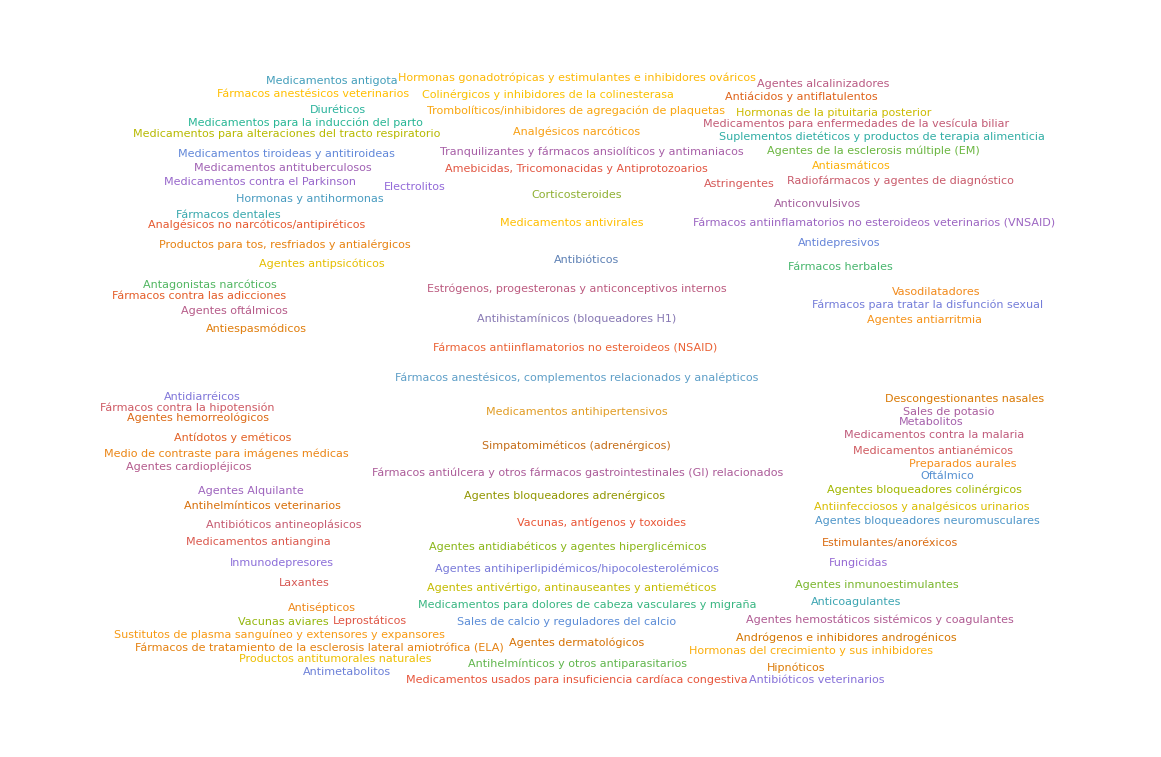

```mathematica
medicamentosDB[WordCloud[Values[#]]&,{"medicamentos"->Length@*Values}]
```

## Export ‘clases de medicamentos’ to xlsx file

```mathematica
Normal@medicamentosDB[All,"clase"]
```

{Antibióticos,Amebicidas, Tricomonacidas y Antiprotozoarios,Antihelmínticos y otros antiparasitarios,Fungicidas,Medicamentos contra la malaria,Medicamentos antituberculosos,Leprostáticos,Antiinfecciosos y analgésicos urinarios,Medicamentos antivirales,Oftálmico,Antihelmínticos veterinarios,Antibióticos veterinarios,Antisépticos,Agentes Alquilante,Antimetabolitos,Antibióticos antineoplásicos,Hormonas y antihormonas,Productos antitumorales naturales,Agentes antiarritmia,Medicamentos antiangina,Medicamentos antihipertensivos,Agentes antihiperlipidémicos/hipocolesterolémicos,Medicamentos usados para insuficiencia cardíaca congestiva,Vasodilatadores,Fármacos contra la hipotensión,Agentes cardiopléjicos,Medicamentos antianémicos,Anticoagulantes,Trombolíticos/inhibidores de agregación de plaquetas,Agentes hemostáticos sistémicos y coagulantes,Sustitutos de plasma sanguíneo y extensores y expansores,Agentes hemorreológicos,Anticonvulsivos,Antidepresivos,Agentes antipsicóticos,Hipnóticos,Tranquilizantes y fármacos ansiolíticos y antimaniacos,Analgésicos no narcóticos/antipiréticos,Fármacos antiinflamatorios no esteroideos (NSAID),Analgésicos narcóticos,Antagonistas narcóticos,Medicamentos para dolores de cabeza vasculares y migraña,Medicamentos contra el Parkinson,Estimulantes/anoréxicos,Fármacos antiinflamatorios no esteroideos veterinarios (VNSAID),Fármacos de tratamiento de la esclerosis lateral amiotrófica (ELA),Fármacos anestésicos, complementos relacionados y analépticos,Colinérgicos y inhibidores de la colinesterasa,Agentes bloqueadores colinérgicos,Simpatomiméticos (adrenérgicos),Agentes bloqueadores adrenérgicos,Agentes bloqueadores neuromusculares,Antiasmáticos,Antihistamínicos (bloqueadores H1),Medicamentos para alteraciones del tracto respiratorio,Productos para tos, resfriados y antialérgicos,Descongestionantes nasales,Antiácidos y antiflatulentos,Laxantes,Antidiarréicos,Agentes antivértigo, antinauseantes y antieméticos,Fármacos antiúlcera y otros fármacos gastrointestinales (GI) relacionados,Medicamentos para enfermedades de la vesícula biliar,Antiespasmódicos,Agentes antidiabéticos y agentes hiperglicémicos,Medicamentos tiroideas y antitiroideas,Corticosteroides,Estrógenos, progesteronas y anticonceptivos internos,Hormonas gonadotrópicas y estimulantes e inhibidores ováricos,Andrógenos e inhibidores androgénicos,Hormonas de la pituitaria posterior,Medicamentos para la inducción del parto,Hormonas del crecimiento y sus inhibidores,Sales de calcio y reguladores del calcio,Diuréticos,Electrolitos,Agentes alcalinizadores,Sales de potasio,Suplementos dietéticos y productos de terapia alimenticia,Inmunodepresores,Vacunas, antígenos y toxoides,Vacunas aviares,Agentes inmunoestimulantes,Agentes de la esclerosis múltiple (EM),Medicamentos antigota,Antídotos y eméticos,Fármacos anestésicos veterinarios,Fármacos herbales,Fármacos dentales,Fármacos contra las adicciones,Radiofármacos y agentes de diagnóstico,Fármacos para tratar la disfunción sexual,Medio de contraste para imágenes médicas,Preparados aurales,Agentes oftálmicos,Agentes dermatológicos,Astringentes,Metabolitos}

```mathematica
SetDirectory["/Users/antonio/Documents/Personal/FSA-CSA/sat to wolfram/"]
```

/Users/antonio/Documents/Personal/FSA-CSA/sat to wolfram

```mathematica
Export["med_clases_export.xlsx",Normal@medicamentosDB[All,"clase"]]
```

med_clases.xlsx